```mathematica
(*反時計まわりが正か負か，人によってことなる．
反時計回りが正のことが多いようなので，ここでもそのように決める*)
```

### 回転行列

```mathematica
Clear["Global`*"];
Rs[{a_,b_,c_,d_}]:=Module[{ind,s,a2,b2,c2,d2},
a2=a*a;
b2=b*b;
c2=c*c;
d2=d*d;
(*s=1/(a*a+b*b+c*c+d*d);*)
(*{{-2*s*(c2+d2),
2*s*(b*c-d*a),
2*s*(b*d+c*a)},
{2*s*(b*c+d*a),
-2*s*(b2+d2),
2*s*(c*d-b*a)},
{2*s*(b*d-c*a),
2*s*(c*d+b*a),
-2*s*(b2+c2)}}*)
s=1;
(*{{-2*s*(c2+d2),
2*s*(b*c-d*a),
2*s*(b*d+c*a)},
{2*s*(b*c+d*a),
-2*s*(b2+d2),
2*s*(c*d-b*a)},
{2*s*(b*d-c*a),
2*s*(c*d+b*a),
-2*s*(b2+c2)}}*)
(*{{a2+b2-c2-d2,2*b*c-2a*d,2b*d+2a*c},
{2b*c+2a*d,a2-b2+c2-d2,2c*d-2a*b},
{2b*d-2a*c,2c*d+2a*b,a2-b2-c2+d2}}*)
{{a2+b2-c2-d2,2*b*c+2*a*d,-2*a*c+2*b*d},
{2*b*c-2*a*d,a2-b2+c2-d2,2*a*b+2*c*d},
{2*a*c+2*b*d,-2*a*b+2*c*d,a2-b2-c2+d2}}
];
Rv[{a_,b_,c_,d_}]=Inverse@Rs[{a,b,c,d}];

AxisAngleToQuaternion[{axX_,axY_,axZ_},angle_]:=Module[{n},
n=Normalize[{axX,axY,axZ}];
Return[{Cos[-angle/2],n[[1]]*Sin[-angle/2],n[[2]]*Sin[-angle/2],n[[3]]*Sin[-angle/2]}];
]
(*IDEN ={{1,0,0},{0,1,0},{0,0,1}};
S[{a_,b_,c_,d_}]:=1/Sqrt[(a*a+b*b+c*c+d*d)];
R[{a_,b_,c_,d_}]:=IDEN+R0[{a,b,c,d}]*S[{a,b,c,d}];*)
rep={a^2->a2,b^2->b2,d^2->d2,c^2->c2,
a^3->a3,b^3->b3,d^3->d3,c^3->c2,
(a2 + b2 + c2 + d2)->a2b2c2d2,
u0^2->u02,u1^2->u12,u2^2->u22,u3^2->u32,u4^2->u42,u5^2->u52,gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2->normGM2,Power->pow};

R[{a_,b_,c_,d_}]:=Rs[{a,b,c,d}];

Tmag = {{Tmag00,Tmag01,Tmag02},
{Tmag10,Tmag11,Tmag12},
{Tmag20,Tmag21,Tmag22}};

Tmag={{1,0,0},{0,1,0},{0,0,1}};

RR[{a_,b_,c_,d_}]:=Module[{zeros,r},
zeros=Table[Table[0,{i,0,2,1}],{j,0,2,1}];
r=Rs[{a,b,c,d}];(*ベクトルを回転する行列*)
Join[Join[r,zeros,2],Join[zeros,Dot[r,Tmag],2]]
]
```

```mathematica
(*磁場センサーのキャリブレーション*)
(*InitM= {InitMx,InitMy,InitMz}*)
{bx,by,bz}={1.22,1.32,0.62}
{Mx0,My0,Mz0}={-11.54,-12.3,-8.2}
{Mx1,My1,Mz1}={-11.8,-12.6,-4.1}
{Mx2,My2,Mz2}={-14.6,-8.1,-4.8}

InitM={Mx0,My0,Mz0}; {InitMx,InitMy,InitMz}

InvRs0=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},0/180*Pi]]
InvRs1=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},120/180*Pi]]
InvRs2=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},240/180*Pi]]


Mb[{Mx_,My_,Mz_}]:={{Mx-bx,My-by,Mz-bz,0,0,0,0,0,0},
{0,0,0,Mx-bx,My-by,Mz-bz,0,0,0},
{0,0,0,0,0,0,Mx-bx,My-by,Mz-bz}}

MatrxMb=Join[Mb[{Mx0,My0,Mz0}],
Mb[{Mx1,My1,Mz1}],
Mb[{Mx2,My2,Mz2}]]

RsInitM=Join[Dot[InvRs0,InitM],
Dot[InvRs1,InitM],
Dot[InvRs2,InitM]]

FullSimplify@Dot[Inverse[MatrxMb],RsInitM]
```

{1.22,1.32,0.62}

{-11.54,-12.3,-8.2}

{-11.8,-12.6,-4.1}

{-14.6,-8.1,-4.8}

{InitMx,InitMy,InitMz}

{{1,0,0},{0,1,0},{0,0,1}}

{{0,1,0},{0,0,1},{1,0,0}}

{{0,0,1},{1,0,0},{0,1,0}}

{{-12.76,-13.62,-8.82,0,0,0,0,0,0},{0,0,0,-12.76,-13.62,-8.82,0,0,0},{0,0,0,0,0,0,-12.76,-13.62,-8.82},{-13.02,-13.92,-4.72,0,0,0,0,0,0},{0,0,0,-13.02,-13.92,-4.72,0,0,0},{0,0,0,0,0,0,-13.02,-13.92,-4.72},{-15.82,-9.42,-5.42,0,0,0,0,0,0},{0,0,0,-15.82,-9.42,-5.42,0,0,0},{0,0,0,0,0,0,-15.82,-9.42,-5.42}}

{-11.54,-12.3,-8.2,-12.3,-8.2,-11.54,-8.2,-11.54,-12.3}

{0.0197872,0.905085,-0.117885,0.532323,-0.253073,1.01524,0.875692,0.260873,-0.740014}

### 姿勢の計算の関数

```mathematica
(*満たすべき方程式*)
Q=Table[q[i],{i,0,3,1}];
{v0[0],v0[1],v0[2],v0[3],v0[4],v0[5]}={gx0,gy0,gz0,mx0,my0,mz0};(*物体の加速度を無視し，重力加速度だけがかかっている．実際は{gx0,gy0,gz0}に物体の加速度がかかっている*)
{u[0],u[1],u[2],u[3],u[4],u[5]}={Ax,Ay,Az,Mx,My,Mz};(*sensor value*)


Print["RR(q)=RR({a,b,c,d})=",RR[{a,b,c,d}]//MatrixForm]
(*関数*)

originalEq[{a_,b_,c_,d_}]=Module[{},
Table[(u[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}]
];
CForm[FullSimplify[originalEq[{a,b,c,d}]]]/.rep/.rep/.Power->pow


f[{a_,b_,c_,d_}]=Sum[(u[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}]/4(*+(1-Sqrt[a^2+b^2+c^2+d^2])*);
(*最小にする関数の微分*)
F[{a_,b_,c_,d_}]=Simplify@{
D[f[{A,b,c,d}],A]/.{A->a},
D[f[{a,B,c,d}],B]/.{B->b},
D[f[{a,b,C,d}],C]/.{C->c},
D[f[{a,b,c,dd}],dd]/.{dd->d}
};
(*最小にする関数の微分の微分*)
DF[{a_,b_,c_,d_}]=Simplify[{
D[F[{A,b,c,d}],A]/.{A->a},
D[F[{a,B,c,d}],B]/.{B->b},
D[F[{a,b,C,d}],C]/.{C->c},
D[F[{a,b,c,dd}],dd]/.{dd->d}}];

Fmod[{a_,b_,c_,d_},A_,M_]:=F[{a,b,c,d}]/.{Ax->A[[1]],Ay->A[[2]],Az->A[[3]],Mx->M[[1]],My->M[[2]],Mz->M[[3]]}
DFmod[{a_,b_,c_,d_},A_,M_]:=DF[{a,b,c,d}]/.{Ax->A[[1]],Ay->A[[2]],Az->A[[3]],Mx->M[[1]],My->M[[2]],Mz->M[[3]]}
```

RR(q)=RR({a,b,c,d})=(a^2+b^2-c^2-d^2 | 2 b c+2 a d | -2 a c+2 b d | 0 | 0 | 0
2 b c-2 a d | a^2-b^2+c^2-d^2 | 2 a b+2 c d | 0 | 0 | 0
2 a c+2 b d | -2 a b+2 c d | a^2-b^2-c^2+d^2 | 0 | 0 | 0
0 | 0 | 0 | a^2+b^2-c^2-d^2 | 2 b c+2 a d | -2 a c+2 b d
0 | 0 | 0 | 2 b c-2 a d | a^2-b^2+c^2-d^2 | 2 a b+2 c d
0 | 0 | 0 | 2 a c+2 b d | -2 a b+2 c d | a^2-b^2-c^2+d^2)

List(pow(Ax - a2*gx0 - b2*gx0 + (c2 + d2)*gx0 + a*(-2*d*gy0 + 2*c*gz0) - 2*b*(c*gy0 + d*gz0),2),
   pow(Ay + 2*a*d*gx0 - a2*gy0 + b2*gy0 - c2*gy0 + d2*gy0 - 2*c*d*gz0 - 2*b*(c*gx0 + a*gz0),2),
   pow(Az - 2*(a*c*gx0 + b*d*gx0 - a*b*gy0 + c*d*gy0) + (-a2 + b2 + c2 - d2)*gz0,2),
   pow(Mx - a2*mx0 - b2*mx0 + (c2 + d2)*mx0 + a*(-2*d*my0 + 2*c*mz0) - 2*b*(c*my0 + d*mz0),2),
   pow(2*a*d*mx0 + My - a2*my0 + b2*my0 - c2*my0 + d2*my0 - 2*c*d*mz0 - 2*b*(c*mx0 + a*mz0),2),
   pow(-2*(a*c*mx0 + b*d*mx0 - a*b*my0 + c*d*my0) + Mz + (-a2 + b2 + c2 - d2)*mz0,2))

```mathematica
yaw[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*d+b*c)/(1-2*(c*c+d*d))]
roll[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*b+c*d)/(1-2*(b*b+c*c))]
pitch[{a_,b_,c_,d_}]:=N@ArcSin[2*(a*c-b*d)]

(*初期姿勢の静止姿勢で観測される重力加速度と磁場を設定．これはfusionの初期に一つ決める値で，DFやFに組み込まれる*)
(****************************************************)
θ=-54/180*Pi;
{gx0,gy0,gz0}={0,0,-1};(*g0*)
{mx0,my0,mz0}={Cos[θ],0,Sin[θ]};(*m0*)
(****************************************************)
getQ[A_,M_]:=Module[{data,abcd,dq,DQ,a,b,c,d,Ax,Ay,Az,Mx,My,Mz},
(****************************************************)
(*模擬した値を与えて正しい結果が得られるかチェック*)
(*rep={u0->A[[1]],u1->A[[2]],u2->A[[3]],u3->M[[1]],u4->M[[2]],u5->M[[3]]}*)
rep={Ax->A[[1]],Ay->A[[2]],Az->A[[3]],Mx->M[[1]],My->M[[2]],Mz->M[[3]]};
(*Print["Rvを使って回転させた加速度Aと磁場Mを与える．",N[dθ]/Pi*180,"度となるはず"];
*)
data={};
abcd={};
dq={1,0,0,0};
DQ={};
{a,b,c,d}={RandomReal[],RandomReal[],RandomReal[],RandomReal[]};
Do[
(*Print[{a,b,c,d}];*)
If[Mod[i,1],{a,b,c,d}=Normalize[{a,b,c,d}];];
(*{a,b,c,d}=Normalize[{a,b,c,d}];*)
dq=(Dot[Inverse[DFmod[{a,b,c,d},A,M]],Fmod[{a,b,c,d},A,M]]);
{a,b,c,d}-=dq;
AppendTo[data,Fmod[{a,b,c,d},A,M]];
AppendTo[DQ,dq];
AppendTo[abcd,{a,b,c,d}];
,{i,0,20,1}];
Return[{a,b,c,d}];
]
```

### 姿勢の計算１：物体の加速度を無視し，重力加速度だけがかかっているとして，物体の姿勢を計測する方法

```mathematica
(*上で設定した，初期のgとmを回転させることで，センサーの値を模擬*)
(****************************************************)
{axis,dθ}={{0,0,1},70/180.*Pi};
q=AxisAngleToQuaternion[axis,dθ];(*この回転を表すクォータニオン*)
A=Dot[Rs[q],{gx0,gy0,gz0}];(*加速度 g^*)
M=Dot[Rs[q],{mx0,my0,mz0}](*磁場 m^*)
```

{0.201034,0.552337,-0.809017}

```mathematica
{a,b,c,d}=getQ[A,M]
```

{0.490655,-0.22768,-0.159424,0.700728}

```mathematica
{a,b,c,d}=getQ[A,M];
Norm[{a,b,c,d}]
(*{a,b,c,d}=Normalize[{a,b,c,d}]*)
(*l=A*)
(*solution={Cos[θ/2.],l[[1]]*Sin[θhorion/2],l[[2]]*Sin[θhorion/2.],l[[3]]*Sin[θhorion/2.]}*)
Print["{Y,P,R}=",{yaw[{a,b,c,d}],roll[{a,b,c,d}],pitch[{a,b,c,d}](*,2ArcTan[Norm[{b,c,d}]/a]*)}/Pi*180]
```

1.

{Y,P,R}={-70.,-5.30364×10^-16,-1.01445×10^-15}

### チェック

```mathematica
Clear[a,b,c,d]
Print["空間を回転させる回転行列"]
Print[CForm[Rs[{a,b,c,d}]/.rep]]
Print["空間を固定しベクトルを回転させる回転行列"]
Print[CForm[Transpose[Rs[{a,b,c,d}]/.rep]]]
N@R[Normalize@{4,1,2,3}]
```

空間を回転させる回転行列

List(List(Power(a,2) + Power(b,2) - Power(c,2) - Power(d,2),2*b*c + 2*a*d,-2*a*c + 2*b*d),List(2*b*c - 2*a*d,Power(a,2) - Power(b,2) + Power(c,2) - Power(d,2),2*a*b + 2*c*d),List(2*a*c + 2*b*d,-2*a*b + 2*c*d,Power(a,2) - Power(b,2) - Power(c,2) + Power(d,2)))

空間を固定しベクトルを回転させる回転行列

List(List(Power(a,2) + Power(b,2) - Power(c,2) - Power(d,2),2*b*c - 2*a*d,2*a*c + 2*b*d),List(2*b*c + 2*a*d,Power(a,2) - Power(b,2) + Power(c,2) - Power(d,2),-2*a*b + 2*c*d),List(-2*a*c + 2*b*d,2*a*b + 2*c*d,Power(a,2) - Power(b,2) - Power(c,2) + Power(d,2)))

{{0.133333,0.933333,-0.333333},{-0.666667,0.333333,0.666667},{0.733333,0.133333,0.666667}}

### 姿勢の計算

```mathematica
(*.08加速度をいっぺんに計算する*)
```

```mathematica
(*データの読み込み*)
```

period→0.005
gyro→{-0.389313,-0.0229008,-0.137405}
accel→{0.0349121,0.0178223,-1.01123}
dt→0.017171
mag→{-2.46735,3.0954,1.65985}
time_ns→42322078000

21161039/500000

-Graphics3D-

-Graphics3D-

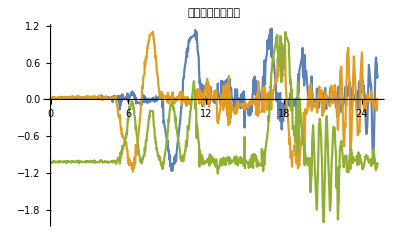

```mathematica
imported =Import[FileNameJoin["/Users/tomoaki/Dropbox/markdown/python_shared/example_AHRS/dataAHRS.json"]];
Column@imported[[1]](*例*)
rowGyros=("mag"/.#5)&@@@imported;
rowAccel=("accel"/.#3)&@@@imported;
rowQuaternion=Quiet[getQ["accel"/.#3,"mag"/.#5]&@@@imported];
starttime=("time_ns"/.#6)*10^-9&@@imported[[1]]
rowAccelX={("time_ns"/.#6)*10^-9-starttime,("accel"/.#3)[[1]]}&@@@imported;
rowAccelY={("time_ns"/.#6)*10^-9-starttime,("accel"/.#3)[[2]]}&@@@imported;
rowAccelZ={("time_ns"/.#6)*10^-9-starttime,("accel"/.#3)[[3]]}&@@@imported;

ListPointPlot3D[rowGyros,BoxRatios->{1, 1, 1},PlotLabel->"磁気データ"]
ListPointPlot3D[rowAccel,BoxRatios->{1, 1, 1},PlotLabel->"加速度データ"]

ListPlot[{rowAccelX,rowAccelY,rowAccelZ},Joined->True,PlotLabel->"加速度成分データ"]
```

General::munfl: 2.68995×10^-284 2.68995×10^-284は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: 1.12825×10^-277 (-1.12825×10^-277)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: -1.12825×10^-277 (-1.12825×10^-277)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

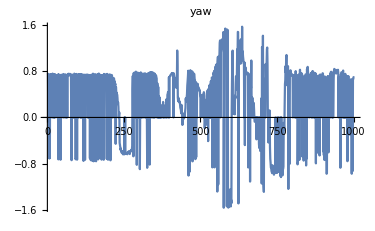

General::munfl: 1.12825×10^-277 5.64123×10^-278は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: 1.12825×10^-277 (-5.64123×10^-278)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: -1.37725×10^-281 (-2.75451×10^-281)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

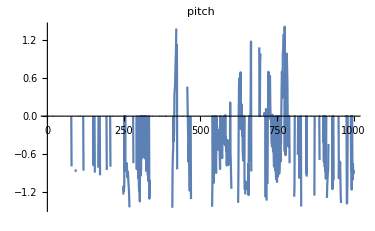

General::munfl: -1.12825×10^-277 5.64123×10^-278は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: 1.12825×10^-277 1.12825×10^-277は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: -1.12825×10^-277 (-1.12825×10^-277)は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

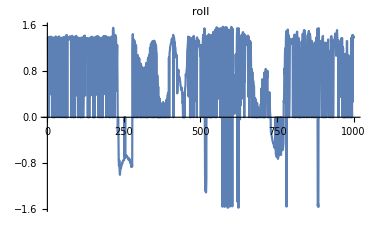

```mathematica
ListPlot[yaw[{#1,#2,#3,#4}]&@@@rowQuaternion,Joined->True,PlotLabel->"yaw"]
ListPlot[pitch[{#1,#2,#3,#4}]&@@@rowQuaternion,Joined->True,PlotLabel->"pitch"]
ListPlot[roll[{#1,#2,#3,#4}]&@@@rowQuaternion,Joined->True,PlotLabel->"roll"]
```

```mathematica
(*(*回転について*)
Rx[t_]:={{1,0,0},{0,Cos[t],Sin[t]},{0,-Sin[t],Cos[t]}}
Ry[t_]:={{Cos[t],0,-Sin[t]},{0,1,0},{Sin[t],0,Cos[t]}}
Rz[t_]:={{Cos[t],-Sin[t],0},{Sin[t],Cos[t],0},{0,0,1}}*)
```

```mathematica
(*(*z->x->zオイラー角*)
Dot[Rz[t3],Dot[Rx[t2],Rz[t1]]]//MatrixForm
(*ヨー->ピッチ->ロール角*)
Dot[Rx[t3],Dot[Ry[t2],Rz[t1]]]//MatrixForm*)
```

```mathematica
(*(*オイラー角*)
Dot[Rz[γ],Dot[Rx[β],Rz[α]]]//MatrixForm
(*ヨーピッチロール角*)
Dot[Rx[ϕ],Dot[Ry[θ],Rz[ψ]]]//MatrixForm*)
```

```mathematica
(*磁場センサーのキャリブレーション*)
(*InitM= {InitMx,InitMy,InitMz}*)
(*imported =Import[FileNameJoin[{NotebookDirectory[],"/dataAHRS.json"}]];*)
imported =Import[FileNameJoin["/Users/tomoaki/Dropbox/markdown/python_shared/example_AHRS/dataAHRS.json"]];
rowGyros=("mag"/.#5)&@@@imported;

minmaxx=MinMax[Transpose[rowGyros][[1]]]
minmaxy=MinMax[Transpose[rowGyros][[2]]]
minmaxz=MinMax[Transpose[rowGyros][[3]]]

bx=Mean@MinMax[Transpose[rowGyros][[1]]]
by=Mean@MinMax[Transpose[rowGyros][[2]]]
bz=Mean@MinMax[Transpose[rowGyros][[3]]]

xyz0={3.228119,1.428089,-0.1646344};
zxy0={1.709656,-4.774952,0.3312323};
yzx0={-3.148223,-1.231832,2.327193};
xyz1={2.509454,-0.3869823,-4.416062};
zxy1={-0.7328072,-1.283755,0.2551079};
yzx1={-3.31675,-0.01326677,-0.3701058};

data={xyz0,zxy0,yzx0,xyz1,zxy1,yzx1};


{Mx0,My0,Mz0}=xyz0
{Mx1,My1,Mz1}=zxy0
{Mx2,My2,Mz2}=yzx0

InitM={Mx0,My0,Mz0}; {InitMx,InitMy,InitMz}

InvRs0=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},0/180*Pi]]
InvRs1=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},-120/180*Pi]]
InvRs2=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},-240/180*Pi]]


Mb[{Mx_,My_,Mz_}]:={{Mx-bx,My-by,Mz-bz,0,0,0,0,0,0},
{0,0,0,Mx-bx,My-by,Mz-bz,0,0,0},
{0,0,0,0,0,0,Mx-bx,My-by,Mz-bz}}

MatrxMb=Join[Mb[{Mx0,My0,Mz0}],
Mb[{Mx1,My1,Mz1}],
Mb[{Mx2,My2,Mz2}]]

RsInitM=Join[Dot[InvRs0,InitM],
Dot[InvRs1,InitM],
Dot[InvRs2,InitM]]

MT=FullSimplify@Dot[Inverse[MatrxMb],RsInitM](*modificationMatrix*)
```

{-2.34772,0.478516}

{-0.643005,2.12341}

{0.628052,3.30475}

-0.934601

0.740204

1.9664

{3.22812,1.42809,-0.164634}

{1.70966,-4.77495,0.331232}

{-3.14822,-1.23183,2.32719}

{InitMx,InitMy,InitMz}

{{1,0,0},{0,1,0},{0,0,1}}

{{0,0,1},{1,0,0},{0,1,0}}

{{0,1,0},{0,0,1},{1,0,0}}

{{4.16272,0.687885,-2.13103,0,0,0,0,0,0},{0,0,0,4.16272,0.687885,-2.13103,0,0,0},{0,0,0,0,0,0,4.16272,0.687885,-2.13103},{2.64426,-5.51516,-1.63517,0,0,0,0,0,0},{0,0,0,2.64426,-5.51516,-1.63517,0,0,0},{0,0,0,0,0,0,2.64426,-5.51516,-1.63517},{-2.21362,-1.97204,0.360793,0,0,0,0,0,0},{0,0,0,-2.21362,-1.97204,0.360793,0,0,0},{0,0,0,0,0,0,-2.21362,-1.97204,0.360793}}

{3.22812,1.42809,-0.164634,-0.164634,3.22812,1.42809,1.42809,-0.164634,3.22812}

{-2.0789,0.626294,-5.37352,0.431048,-0.392081,0.0452995,-2.03202,-0.0723346,-3.91539}

```mathematica
magModified[mag_]:=Module[{},
(*Return@Dot[{{RsInitM[[1]],RsInitM[[2]],RsInitM[[3]]},
{RsInitM[[4]],RsInitM[[5]],RsInitM[[6]]},
{RsInitM[[7]],RsInitM[[8]],RsInitM[[9]]}},
{mag[[1]]-bx,mag[[2]]-by,mag[[3]]-bz}]*)
Return@{mag[[1]]-bx,mag[[2]]-by,mag[[3]]-bz};
]
```

```mathematica
mags=magModified[("mag"/.#5)]&@@@imported;
ListPointPlot3D[mags,BoxRatios->{1, 1, 1}]

Print["minmax=",{minmaxx,minmaxy,minmaxz}]
Print["bias=",{bx,by,bz}]
Print["MT=",MT]
```

-Graphics3D-

minmax={{-2.34772,0.478516},{-0.643005,2.12341},{0.628052,3.30475}}

bias={-0.934601,0.740204,1.9664}

MT={-2.0789,0.626294,-5.37352,0.431048,-0.392081,0.0452995,-2.03202,-0.0723346,-3.91539}